## Archived Code

### Symmetry Axis

```mathematica
(* 
(* findSym is Implemented from Jens *)
findSym[mask_,option_:False]:=Block[{imd,nx,ny,points,weights,mass,centerOfMass,pointsCom,diag,inertia,v1,v2},
imd=Transpose@ImageData[mask];(* here we transpose the image data *)
{nx,ny}=Dimensions[imd];(* dimensions of the image *)
points=Tuples[{Range[nx],Reverse@Range[ny]}]; (* x-y coordinates on the image *)
weights=Flatten[imd]; (* vector of imagedata *)

centerOfMass=ImageMeasurements[mask,"IntensityCentroid"];(* here we calculate the x-y coordinate of the center of mass *)

pointsCom=(Subtract[#,centerOfMass]&/@points) weights; 
(* we subtract from each point the center of mass. 
This gives us a vector of n number of points the {x,y} coordinates of which are displacements from the centroids.
 We multiply this resulting matrix with the intensity vector. This gives us a vector consisting of two coordinates,
 which are x y displacments from centroid * intensity for each point in the grid *)

diag=Total[(#.#)&/@pointsCom]; (* sum of the {x,y}.{x,y} from above. gives a single values *)
inertia=Table[KroneckerDelta[i,j] diag-Total[(#[[i]] #[[j]])&/@pointsCom],{i,2},{j,2}]; (* inertia *)

{v1,v2}=Eigenvectors[inertia]; (* extracting eigenvectors from inertia *)
(* Print["center of Mass: ", centerOfMass,"\n","pt1 : ",v1 + centerOfMass,"\n","pt2 : ",v2 + centerOfMass]; *)
(* display *)
If[option,Print@Show[mask,Graphics[{{Thick,Dashed,XYZColor[0,0,1,0.6],InfiniteLine[{v2+centerOfMass,centerOfMass}]},
{Thick,Dashed,XYZColor[1,0,0,0.6],InfiniteLine[{v1+centerOfMass,centerOfMass}]},
{Darker@XYZColor[0,1,0,0.5],PointSize[Large],Point[centerOfMass]},Red,Point[v1+centerOfMass],Blue,Point[v2+centerOfMass]}]]
];
{centerOfMass,v1,v2}
]
*)
```

### mask to region/shortest tour for boundary

```mathematica
(*
(*given a mask -> find shortest tour and convert to region *)
convertToRegion[mask_]:= Block[{pixelvaluepos,tour,pixelposordered},
pixelvaluepos= PixelValuePositions[MorphologicalPerimeter@mask,1];
tour=Last@FindShortestTour[pixelvaluepos];
pixelposordered = Part[pixelvaluepos,tour];
{pixelposordered,BoundaryMeshRegion[N@pixelvaluepos,Line@tour]}
]
*)
```

### bisect region

```mathematica
(*
bisectReg[mask_, options_:False]:= Block[{centerofMass,v1,v2,pixelordered,ℛ1,ℛ2,pt1,pt2,list,
trimList,npixelordered,nf, ptslocation,firstPreMask,secondPreMask,imgDim1, imgDim2},
{imgDim1,imgDim2}=ImageDimensions@mask;

{centerofMass,v1,v2} = findSym[mask];
{pixelordered,ℛ1}=convertToRegion[mask];
ℛ2=InfiniteLine[{centerofMass,centerofMass+v1}];
list=(RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1]//Cases[#,Point[arg_]:> arg]&);

trimList[ls_]:= Module[{p=ls,pairs,firstelem = First@ls,dist,maxdist},
pairs={firstelem,#}&/@p;
dist=EuclideanDistance[##]&@@@pairs;
maxdist=Max@dist;
pairs[[First@@Position[dist,maxdist]]]
]/;Length@ls>2;

{pt1,pt2}=trimList[list]/.trimList[arg__]:> arg;

If[options, Print@Show[HighlightMesh[ℛ1,{Style[1,Directive[XYZColor[0,0,1,0.9]]],Style[2,Directive[XYZColor[0,0,1,0.18]]]}],
Graphics[{Red,PointSize[Large],Point@pt1,PointSize[Large],Darker@Green,Point@pt2,Thick,Dashed,XYZColor[1,0,0,0.5],ℛ2,Blue,Point@centerofMass}]]
];

Join[{centerofMass},pt1,pt2]
]
*)
```

### elongation

```mathematica
(*
Options[Elong]={"div"-> 5, "printBisect" -> False};
Elong[mask_,OptionsPattern[]]:=With[{div=OptionValue["div"], printBisect=OptionValue["printBisect"]},
Block[{p,centroid,pt1,pt2,boundary,tour,boundaryc,nF,ℛ1,ℛ2,intersections,rotationTransform,pts,
θ,r,infinitelines,contour,surfacepts,pos,surfacepts2,surfacepts3,diameter,perimeter,area,elongation},
{centroid,pt1,pt2}=bisectReg[mask,printBisect];
boundary=PixelValuePositions[MorphologicalPerimeter@mask,1];
tour=Last@FindShortestTour[boundary];
boundaryc=Part[boundary,tour];
nF=Nearest[boundaryc]; (* Nearest Function *)
ℛ1=BoundaryMeshRegion[boundary,Line@tour]; (* boundary *)
ℛ2=InfiniteLine[{centroid,pt1}]; (* pseudo axis of symmetry *)
intersections=Cases[RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1],_Point]/.Point[{x_}]:> x;
rotationTransform=RotationTransform[div Degree,centroid];
pts=Rest@NestList[rotationTransform,pt1,360/(div*2)];
infinitelines=InfiniteLine[{centroid,#}]&/@pts;
contour= Polygon@boundaryc;
(*surfacepts=(x↦RegionIntersection[x,contour])/@infinitelines/.Point[x_]:>x; *)
surfacepts = Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],contour,#}]]&/@infinitelines;
pos = Position[surfacepts,_?(Length@#>2&),{1}];
surfacepts2=MapAt[Sequence@@TakeLargestBy[Permutations[#,{2}],EuclideanDistance[#[[1]],#[[2]]]&,1]&,surfacepts,pos];
θ = Array[# &, 360/div,{0, 2π}];
p/:r[p]:= Join[#[[;;,1]],#[[;;,2]]]&@Map[EuclideanDistance[centroid,#]&,surfacepts2,{2}];
diameter=Plus@@Partition[r[p],Length[r[p]]/2];
{perimeter,area,elongation}=Values@@ComponentMeasurements[mask,{"PerimeterLength","Area","Elongation"}];
{perimeter,area,elongation,MinMax@diameter, MinMax@r[p]}
]
];
*)
```

### MSD

```mathematica
(*
ClearAll@MSD;
MSD[ptslist_,ntime_:2]:=Module[{},
Map[x↦With[{timesteps=Round[Length@ptslist[[x]]/ntime]},
Module[{threadedlist},
threadedlist=Table[Thread[{ptslist[[x]],
RotateLeft[ptslist[[x]],i]}][[;;-(i+1)]],{i,timesteps}];
Mean/@Map[Function[x,Power[#,2]&@
(Norm@(Subtract@@Reverse@x))],threadedlist,{2}]
]
],Range@Length@ptslist]
];
*)
```

## Initialize

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\trajectory in mosaic aggregates\\props.m";
```

## B7

```mathematica
(* from frame 40 to -12 *)
```

```mathematica
images = ImageAdjust/@Import["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\B7\\nuclear-marker-Reg.tif"];
```

```mathematica
imagesLoG = ImageAdjust@LaplacianGaussianFilter[#,5]&/@images;
```

```mathematica
pts = {{248.,296.6666666666667},{227.33333333333331,292.}};
```

```mathematica
pos=Transpose@ImageFeatureTrack[imagesLoG[[40;;-12]],pts,MaxFeatureDisplacement->2];
```

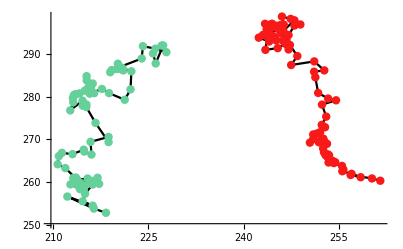

```mathematica
Show@MapThread[ListPlot[#,Joined->#2,PlotStyle->#3]&,{{pos,pos},{True,False},{Black,{{PointSize[0.015],RandomColor[]},{PointSize[0.015],RandomColor[]}}}}]
```

```mathematica
col=ColorData["Rainbow"]/@Rescale@Range@Max@(Length/@pos)
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.4389356455696203, 0.11055111392405063, 0.5548545822784811],RGBColor[0.4064592911392405, 0.11233622784810127, 0.5826931645569621],RGBColor[0.37398293670886074, 0.1141213417721519, 0.6105317468354431],RGBColor[0.341506582278481, 0.11590645569620253, 0.638370329113924],RGBColor[0.31029630379746836, 0.11894463291139241, 0.6657941012658227],RGBColor[0.29807716455696204, 0.14077875949367089, 0.6869957215189874],RGBColor[0.2858580253164557, 0.16261288607594937, 0.7081973417721519],RGBColor[0.2736388860759494, 0.18444701265822785, 0.7293989620253164],RGBColor[0.26141974683544306, 0.20628113924050634, 0.7506005822784809],RGBColor[0.25055969620253166, 0.2288253924050633, 0.7703401518987342],RGBColor[0.2492132658227848, 0.25634053164556964, 0.7798453670886075],RGBColor[0.24786683544303797, 0.28385567088607594, 0.789350582278481],RGBColor[0.24652040506329115, 0.3113708101265823, 0.7988557974683544],RGBColor[0.2451739746835443, 0.3388859493670886, 0.8083610126582279],RGBColor[0.24491703797468353, 0.3660048607594937, 0.815569253164557],RGBColor[0.24938124050632912, 0.3914067848101266, 0.8128239367088608],RGBColor[0.2538454430379747, 0.4168087088607595, 0.8100786202531646],RGBColor[0.25830964556962027, 0.4422106329113924, 0.8073333037974684],RGBColor[0.26277384810126586, 0.4676125569620253, 0.8045879873417722],RGBColor[0.2681370379746836, 0.49167215189873414, 0.7993460632911393],RGBColor[0.27619718987341774, 0.5117047594936709, 0.7866143164556962],RGBColor[0.2842573417721519, 0.5317373670886075, 0.7738825696202533],RGBColor[0.2923174936708861, 0.5517699746835443, 0.7611508227848102],RGBColor[0.30037764556962027, 0.571802582278481, 0.7484190759493672],RGBColor[0.30937222784810126, 0.5900170253164556, 0.7337182784810127],RGBColor[0.3204225569620253, 0.6042315063291139, 0.7146855696202532],RGBColor[0.3314728860759494, 0.6184459873417721, 0.6956528607594937],RGBColor[0.34252321518987344, 0.6326604683544303, 0.6766201518987343],RGBColor[0.3535735443037975, 0.6468749493670886, 0.6575874430379747],RGBColor[0.365748, 0.6592595063291139, 0.6376891392405064],RGBColor[0.379796, 0.6685941898734177, 0.61634817721519],RGBColor[0.393844, 0.6779288734177215, 0.5950072151898734],RGBColor[0.40789200000000003, 0.6872635569620252, 0.573666253164557],RGBColor[0.42194, 0.696598240506329, 0.5523252911392406],RGBColor[0.4372473797468355, 0.7043363037974683, 0.5314922278481014],RGBColor[0.45417396202531646, 0.7100215696202531, 0.51131217721519],RGBColor[0.4711005443037975, 0.7157068354430379, 0.4911321265822785],RGBColor[0.4880271265822785, 0.7213921012658228, 0.4709520759493671],RGBColor[0.5049537088607595, 0.7270773670886076, 0.4507720253164557],RGBColor[0.5229596835443038, 0.7313172658227848, 0.4323686835443038],RGBColor[0.5420450506329114, 0.7341117974683544, 0.4157420506329114],RGBColor[0.5611304177215191, 0.7369063291139241, 0.399115417721519],RGBColor[0.5802157848101266, 0.7397008607594937, 0.3824887848101266],RGBColor[0.5993011518987342, 0.7424953924050632, 0.36586215189873417],RGBColor[0.6187457215189874, 0.7435896075949368, 0.3518185189873418],RGBColor[0.638469670886076, 0.7433613544303798, 0.3397838860759494],RGBColor[0.6581936202531646, 0.7431331012658228, 0.327749253164557],RGBColor[0.6779175696202532, 0.7429048481012658, 0.31571462025316455],RGBColor[0.6976415189873418, 0.7426765949367089, 0.30367998734177215],RGBColor[0.716368506329114, 0.7398779620253164, 0.29431408860759495],RGBColor[0.7344973164556963, 0.7355371012658227, 0.28654943037974684],RGBColor[0.7526261265822785, 0.7311962405063291, 0.27878477215189873],RGBColor[0.7707549367088607, 0.7268553797468355, 0.2710201139240506],RGBColor[0.788883746835443, 0.7225145189873418, 0.2632554556962025],RGBColor[0.8041514430379746, 0.7141420886075949, 0.257450329113924],RGBColor[0.8181186329113923, 0.7039371265822785, 0.2525358987341772],RGBColor[0.83208582278481, 0.693732164556962, 0.24762146835443036],RGBColor[0.8460530126582277, 0.6835272025316456, 0.24270703797468354],RGBColor[0.8600202025316455, 0.6733222405063292, 0.2377926075949367],RGBColor[0.8692085063291138, 0.6574122658227848, 0.2335226835443038],RGBColor[0.8768038481012658, 0.6396006202531646, 0.22946759493670887],RGBColor[0.8843991898734177, 0.6217889746835443, 0.22541250632911392],RGBColor[0.8919945316455696, 0.603977329113924, 0.22135741772151898],RGBColor[0.8995898734177215, 0.5861656835443038, 0.21730232911392405],RGBColor[0.9013166202531645, 0.5616208607594936, 0.21250574683544304],RGBColor[0.9016890759493671, 0.5355222278481012, 0.2075380506329114],RGBColor[0.9020615316455696, 0.5094235949367089, 0.20257035443037974],RGBColor[0.9024339873417722, 0.48332496202531644, 0.1976026582278481],RGBColor[0.9028064430379747, 0.457226329113924, 0.19263496202531644],RGBColor[0.8984676329113924, 0.42547559493670883, 0.18642587341772152],RGBColor[0.8934557848101266, 0.392917417721519, 0.18003944303797467],RGBColor[0.8884439367088608, 0.3603592405063291, 0.17365301265822786],RGBColor[0.8834320886075949, 0.3278010632911392, 0.167266582278481],RGBColor[0.878420240506329, 0.2952428860759494, 0.1608801518987342],RGBColor[0.8741675063291139, 0.26242913924050637, 0.15509751898734178],RGBColor[0.8699653797468354, 0.22959835443037976, 0.14935513924050633],RGBColor[0.8657632531645569, 0.19676756962025319, 0.1436127594936709],RGBColor[0.8615611265822785, 0.16393678481012658, 0.13787037974683544],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
len=Length[col]
```

80

```mathematica
N[119*6./60+72]
```

83.9

```mathematica
BarLegend[{"Rainbow",{76,83.9}},len,LegendLabel->"hr"]
```

```mathematica
Rasterize[
Show[ColorNegate@GaussianFilter[-Graphics-,5],Graphics[{PointSize[0.008],Point[#,VertexColors->Take[col,Length@#]],Line@#}&/@pos]],"Image",ImageResolution->1000
]
```

```mathematica
msds= MSD@pos;
```

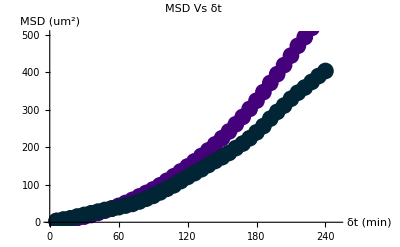

```mathematica
Show[ListPlot[Thread[{Range@Length@#*6,#*2*(0.633^2)}],PlotLabel->Style["MSD Vs δt",Bold,16],AxesLabel->{Style["δt (min)",{Bold,15}],Style["MSD (um^2)",{Bold,15}]},AxesStyle->Directive[Black, 14],PlotStyle->{RandomColor[],PointSize[0.03]},PlotRange->{{0,250},{0,500}}]&/@msds ]
```

```mathematica
(* show cells on the image sequence *)
```

```mathematica
ListAnimate@MapThread[
HighlightImage[#1,{PointSize[0.01],Black,Point@{##2}},ImageSize->Medium]&,
{images[[40;;-12]],pos[[1]],pos[[2]]}]
```

## B8

```mathematica
(* from frame 79 to end *)
```

```mathematica
images=ImageAdjust/@Import["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\B8\\nuclear-marker-Reg.tif"];
```

```mathematica
imagesLoG=ImageAdjust@LaplacianGaussianFilter[GaussianFilter[#,2],5]&/@images;
```

```mathematica
(* ListAnimate@imagesLoG *)
```

```mathematica
imagesLoGtrimmed=imagesLoG[[79;;]];
```

```mathematica
pts={{281.5,331.25},{271.5,325.25},{252.5,309.25},{220.5,281.25}};
```

```mathematica
tracks=Transpose@ImageFeatureTrack[imagesLoGtrimmed,pts,MaxFeatureDisplacement->2];
```

```mathematica
untrimmedlen=First@Union[Length/@tracks];
```

```mathematica
tracks=DeleteMissing/@tracks;
```

```mathematica
trackstrimmed = {tracks[[1]][[;;60]],tracks[[2]][[;;30]],tracks[[3]][[;;-10]],tracks[[4]][[;;-5]]};
```

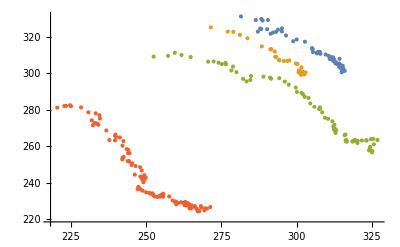

```mathematica
ListPlot[trackstrimmed,PlotRange->All]
```

```mathematica
(* imagesoverlap=MapThread[Show[#1,Graphics[{Red,Point@#2}]]&,{imagesLoGtrimmed[[;;-5]],trackstrimmed[[4]]}]; *)
```

```mathematica
col=ColorData["Rainbow"]/@Rescale@Range@Max@(Length/@trackstrimmed)
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.446009702970297, 0.11016227722772277, 0.5487907326732674],RGBColor[0.42060740594059404, 0.11155855445544555, 0.5705654653465346],RGBColor[0.3952051089108911, 0.11295483168316832, 0.592340198019802],RGBColor[0.36980281188118813, 0.11435110891089109, 0.6141149306930693],RGBColor[0.34440051485148515, 0.11574738613861386, 0.6358896633663367],RGBColor[0.31899821782178217, 0.11714366336633664, 0.6576643960396039],RGBColor[0.30448918811881187, 0.1293212475247525, 0.6758701188118812],RGBColor[0.2949316435643564, 0.14639942574257425, 0.6924535643564356],RGBColor[0.285374099009901, 0.16347760396039604, 0.7090370099009901],RGBColor[0.27581655445544556, 0.18055578217821783, 0.7256204554455445],RGBColor[0.2662590099009901, 0.1976339603960396, 0.7422039009900989],RGBColor[0.25670146534653465, 0.2147121386138614, 0.7587873465346534],RGBColor[0.2503330693069307, 0.23345665346534653, 0.7719400396039603],RGBColor[0.24927992079207922, 0.254978396039604, 0.7793748118811881],RGBColor[0.24822677227722773, 0.2765001386138614, 0.7868095841584158],RGBColor[0.24717362376237623, 0.2980218811881188, 0.7942443564356435],RGBColor[0.24612047524752476, 0.3195436237623762, 0.8016791287128713],RGBColor[0.24506732673267326, 0.34106536633663365, 0.809113900990099],RGBColor[0.24429823762376238, 0.36248380198019803, 0.8159497920792079],RGBColor[0.2477900396039604, 0.38235263366336636, 0.8138024653465347],RGBColor[0.2512818415841584, 0.40222146534653463, 0.8116551386138614],RGBColor[0.25477364356435644, 0.42209029702970297, 0.8095078118811881],RGBColor[0.2582654455445545, 0.4419591287128713, 0.8073604851485149],RGBColor[0.2617572475247525, 0.46182796039603957, 0.8052131584158416],RGBColor[0.26524904950495054, 0.4816967920792079, 0.8030658316831684],RGBColor[0.2708503564356436, 0.498415801980198, 0.7950601287128714],RGBColor[0.27715483168316835, 0.5140848712871287, 0.7851016336633664],RGBColor[0.2834593069306931, 0.5297539405940593, 0.7751431386138614],RGBColor[0.28976378217821785, 0.54542300990099, 0.7651846435643564],RGBColor[0.29606825742574255, 0.5610920792079208, 0.7552261485148515],RGBColor[0.3023727326732673, 0.5767611485148515, 0.7452676534653466],RGBColor[0.30970045544554453, 0.5904392376237624, 0.7331529504950496],RGBColor[0.31834378217821785, 0.601557495049505, 0.7182659801980198],RGBColor[0.3269871089108911, 0.6126757524752475, 0.7033790099009901],RGBColor[0.3356304356435644, 0.6237940099009901, 0.6884920396039604],RGBColor[0.34427376237623764, 0.6349122673267327, 0.6736050693069308],RGBColor[0.3529170891089109, 0.6460305247524752, 0.6587180990099011],RGBColor[0.36185350495049506, 0.6566716732673267, 0.6436054455445545],RGBColor[0.37284154455445545, 0.6639730594059405, 0.6269130099009902],RGBColor[0.38382958415841584, 0.6712744455445544, 0.6102205742574258],RGBColor[0.3948176237623763, 0.6785758316831683, 0.5935281386138614],RGBColor[0.40580566336633667, 0.6858772178217821, 0.5768357029702971],RGBColor[0.41679370297029705, 0.693178603960396, 0.5601432673267327],RGBColor[0.42778174257425744, 0.7004799900990099, 0.5434508316831683],RGBColor[0.4405991782178218, 0.705462099009901, 0.5274961782178218],RGBColor[0.4538387821782178, 0.7099089900990099, 0.5117117821782179],RGBColor[0.46707838613861385, 0.7143558811881188, 0.49592738613861387],RGBColor[0.4803179900990099, 0.7188027722772277, 0.48014299009900996],RGBColor[0.49355759405940597, 0.7232496633663367, 0.46435859405940594],RGBColor[0.506797198019802, 0.7276965544554456, 0.44857419801980203],RGBColor[0.5208810792079208, 0.7310129108910891, 0.43417950495049507],RGBColor[0.5358092376237624, 0.7331987326732673, 0.42117451485148516],RGBColor[0.550737396039604, 0.7353845544554456, 0.40816952475247525],RGBColor[0.5656655544554456, 0.7375703762376238, 0.39516453465346535],RGBColor[0.5805937128712871, 0.739756198019802, 0.38215954455445544],RGBColor[0.5955218712871287, 0.7419420198019802, 0.36915455445544554],RGBColor[0.6105436831683169, 0.7436845247524753, 0.3568230198019802],RGBColor[0.6259713267326733, 0.7435059900990099, 0.3474097920792079],RGBColor[0.6413989702970297, 0.7433274554455446, 0.33799656435643566],RGBColor[0.6568266138613862, 0.7431489207920792, 0.3285833366336634],RGBColor[0.6722542574257426, 0.7429703861386139, 0.3191701089108911],RGBColor[0.6876819009900991, 0.7427918514851485, 0.30975688118811884],RGBColor[0.7031095445544555, 0.7426133168316832, 0.3003436534653465],RGBColor[0.7174454653465347, 0.7396200891089109, 0.29385282178217825],RGBColor[0.7316254257425743, 0.7362247623762376, 0.2877794752475248],RGBColor[0.7458053861386139, 0.7328294356435643, 0.28170612871287126],RGBColor[0.7599853465346534, 0.7294341089108911, 0.2756327821782178],RGBColor[0.7741653069306931, 0.7260387821782178, 0.2695594356435643],RGBColor[0.7883452673267326, 0.7226434554455445, 0.26348608910891086],RGBColor[0.8006942178217821, 0.7166680693069306, 0.2586667722772277],RGBColor[0.8116190495049505, 0.7086859702970297, 0.2548228118811881],RGBColor[0.8225438811881187, 0.7007038712871287, 0.2509788514851485],RGBColor[0.8334687128712871, 0.6927217722772278, 0.2471348910891089],RGBColor[0.8443935445544554, 0.6847396732673268, 0.24329093069306928],RGBColor[0.8553183762376237, 0.6767575742574258, 0.2394469702970297],RGBColor[0.8649972277227722, 0.6672880297029703, 0.23577104950495048],RGBColor[0.8709381386138614, 0.6533561485148515, 0.23259924752475247],RGBColor[0.8768790495049504, 0.6394242673267326, 0.22942744554455446],RGBColor[0.8828199603960396, 0.6254923861386138, 0.22625564356435643],RGBColor[0.8887608712871287, 0.6115605049504951, 0.22308384158415842],RGBColor[0.8947017821782178, 0.5976286237623762, 0.2199120396039604],RGBColor[0.9006426930693069, 0.5836967425742574, 0.21674023762376238],RGBColor[0.9012871188118812, 0.5636880792079207, 0.21289922772277228],RGBColor[0.9015784455445545, 0.543274297029703, 0.20901360396039603],RGBColor[0.9018697722772278, 0.5228605148514851, 0.2051279801980198],RGBColor[0.902161099009901, 0.5024467326732673, 0.20124235643564356],RGBColor[0.9024524257425742, 0.48203295049504946, 0.1973567326732673],RGBColor[0.9027437524752475, 0.4616191683168317, 0.1934711089108911],RGBColor[0.900402900990099, 0.4380475643564356, 0.1888919207920792],RGBColor[0.8964827425742574, 0.41258126732673267, 0.18389659405940595],RGBColor[0.8925625841584158, 0.3871149702970297, 0.17890126732673267],RGBColor[0.8886424257425742, 0.36164867326732675, 0.17390594059405942],RGBColor[0.8847222673267326, 0.33618237623762376, 0.16891061386138614],RGBColor[0.8808021089108911, 0.31071607920792077, 0.1639152871287129],RGBColor[0.8770798712871287, 0.2851831485148515, 0.15907738613861389],RGBColor[0.8737930594059405, 0.25950362376237623, 0.15458582178217822],RGBColor[0.8705062475247525, 0.233824099009901, 0.1500942574257426],RGBColor[0.8672194356435643, 0.20814457425742575, 0.14560269306930693],RGBColor[0.8639326237623762, 0.1824650495049505, 0.1411111287128713],RGBColor[0.860645811881188, 0.15678552475247526, 0.13661956435643563],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
Map[Length]@trackstrimmed
```

{60,30,71,102}

```mathematica
BarLegend[{"Rainbow",{79.9,90.1}},102,LegendLabel->"hr"]
```

```mathematica
Rasterize[
Show[ColorNegate@GaussianFilter[-Graphics-,5],Graphics[{PointSize[0.008],Point[#,VertexColors->Take[col,Length@#]],Line@#}&/@trackstrimmed]],"Image",ImageResolution->1000
]
```

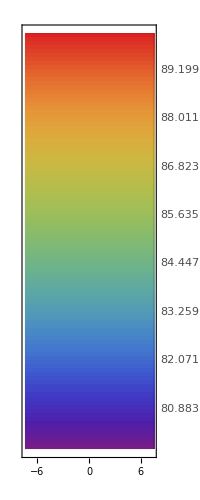
```mathematica
-Graphics-{{hrs}, {-Graphics-}}
```

```mathematica
msds= MSD@trackstrimmed;
```

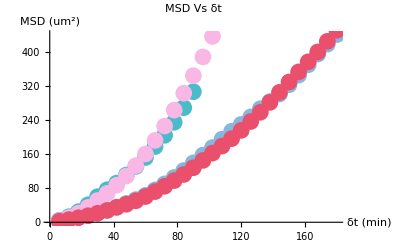

```mathematica
Show[ListPlot[Thread[{Range@Length@#*6,#*2*(0.633^2)}],PlotLabel->Style["MSD Vs δt",Bold,16],AxesLabel->{Style["δt (min)",{Bold,15}],Style["MSD (um^2)",{Bold,15}]},AxesStyle->Directive[Black, 14],PlotStyle->{RandomColor[],PointSize[0.03]}]&/@msds]
```

```mathematica
res=elongation/@{-Graphics-,-Graphics-};
```

```mathematica
Row[{Style["% elongation: ",Bold,RandomColor[]],Abs[Subtract@@#]/Min[#]*100}]&@{Max@#1/Min@#1,Max@#2/Min@#2}&@@res[[All,-1]]
```

% elongation: 11.1574

```mathematica
Row[{Style["% Area increase: ", Bold,RandomColor[]],Abs[Subtract@@#]/First[#]*100}]&@res[[All,2]]
```

% Area increase: 42.3376

```mathematica
(* show cells on the image sequence *)
```

```mathematica
len=Length/@trackstrimmed
```

{60,30,71,102}

```mathematica
array= ConstantArray[0,{4,106}];
array[[1,;;len[[1]] ]]=trackstrimmed[[1,;;len[[1]] ]];
array[[2,;;len[[2]] ]]=trackstrimmed[[2,;;len[[2]] ]];
array[[3,;;len[[3]] ]]=trackstrimmed[[3,;;len[[3]] ]];
array[[4,;;len[[4]] ]]=trackstrimmed[[4,;;len[[4]] ]];
```

```mathematica
ListAnimate@MapThread[
Block[{appendLs={}},
If[#2=!=0,AppendTo[appendLs,#2]];
If[#3=!=0,AppendTo[appendLs,#3]];
If[#4=!=0,AppendTo[appendLs,#4]];
If[#5=!=0,AppendTo[appendLs,#5]];
If[appendLs≠{},
HighlightImage[#1,{PointSize[0.01],Black,Point@appendLs},ImageSize->Medium],
Image[#1,ImageSize->Medium]]
]&,{images[[79;;]],Sequence@@array}]
```

## F10

```mathematica
(* from frame 58 to end *)
```

```mathematica
images=ImageAdjust/@Import["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@mosaic-braNuc and E14TG2A\\F10\\nuclear-marker-Reg.tif"];
```

```mathematica
imagesLoG=ImageAdjust@LaplacianGaussianFilter[#,5]&/@images;
```

```mathematica
(*ListAnimate@imagesLoG*)
```

```mathematica
pts={{215.33333333333331,238.},{253.33333333333331,332.},{220.,219.33333333333331},{212.66666666666663,220.66666666666666}};
```

```mathematica
pos=Transpose@ImageFeatureTrack[imagesLoG[[58;;]],pts,MaxFeatureDisplacement->2];
```

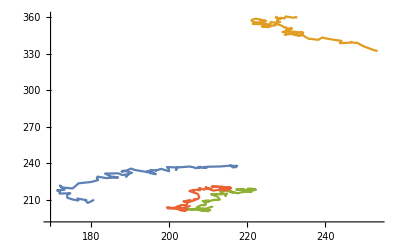

```mathematica
ListPlot[pos[[All,;;80]],Joined-> True,PlotRange->All]
```

```mathematica
col=ColorData["Rainbow"]/@Rescale@Range@Max@(Length/@pos)
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.45104984126984127, 0.10988523809523809, 0.5444703492063492],RGBColor[0.43068768253968254, 0.1110044761904762, 0.5619246984126984],RGBColor[0.4103255238095238, 0.11212371428571428, 0.5793790476190477],RGBColor[0.3899633650793651, 0.11324295238095239, 0.5968333968253968],RGBColor[0.36960120634920635, 0.11436219047619048, 0.6142877460317461],RGBColor[0.3492390476190476, 0.11548142857142857, 0.6317420952380952],RGBColor[0.3288768888888889, 0.11660066666666667, 0.6491964444444445],RGBColor[0.3101023492063492, 0.11929120634920636, 0.6661306349206348],RGBColor[0.30244114285714285, 0.13298085714285715, 0.6794237142857142],RGBColor[0.2947799365079365, 0.14667050793650793, 0.6927167936507936],RGBColor[0.2871187301587302, 0.16036015873015874, 0.706009873015873],RGBColor[0.2794575238095238, 0.17404980952380952, 0.7193029523809523],RGBColor[0.27179631746031746, 0.1877394603174603, 0.7325960317460317],RGBColor[0.2641351111111111, 0.20142911111111111, 0.7458891111111111],RGBColor[0.2564739047619048, 0.21511876190476192, 0.7591821904761904],RGBColor[0.2505169523809524, 0.2296988888888889, 0.7706419047619048],RGBColor[0.2496727619047619, 0.24695044444444444, 0.7766015238095237],RGBColor[0.24882857142857143, 0.264202, 0.7825611428571428],RGBColor[0.24798438095238096, 0.28145355555555557, 0.7885207619047618],RGBColor[0.24714019047619049, 0.2987051111111111, 0.7944803809523809],RGBColor[0.246296, 0.31595666666666666, 0.80044],RGBColor[0.24545180952380952, 0.33320822222222224, 0.806399619047619],RGBColor[0.24460761904761905, 0.3504597777777778, 0.8123592380952381],RGBColor[0.24512961904761904, 0.3672144761904762, 0.8154385238095239],RGBColor[0.24792860317460316, 0.38314107936507935, 0.813717253968254],RGBColor[0.2507275873015873, 0.39906768253968256, 0.8119959841269841],RGBColor[0.25352657142857143, 0.4149942857142857, 0.8102747142857143],RGBColor[0.2563255555555556, 0.4309208888888889, 0.8085534444444444],RGBColor[0.2591245396825397, 0.44684749206349206, 0.8068321746031747],RGBColor[0.26192352380952383, 0.4627740952380952, 0.8051109047619048],RGBColor[0.264722507936508, 0.4787006984126984, 0.803389634920635],RGBColor[0.2686487936507937, 0.4929440634920635, 0.7985376984126985],RGBColor[0.273702380952381, 0.5055041904761904, 0.7905550952380953],RGBColor[0.27875596825396826, 0.5180643174603174, 0.7825724920634921],RGBColor[0.2838095555555556, 0.5306244444444445, 0.7745898888888889],RGBColor[0.2888631428571429, 0.5431845714285714, 0.7666072857142857],RGBColor[0.29391673015873016, 0.5557446984126984, 0.7586246825396826],RGBColor[0.29897031746031744, 0.5683048253968254, 0.7506420793650794],RGBColor[0.3040239047619048, 0.5808649523809524, 0.7426594761904762],RGBColor[0.3102492380952381, 0.5911451587301587, 0.7322077460317461],RGBColor[0.31717761904761904, 0.6000574126984126, 0.7202745396825397],RGBColor[0.324106, 0.6089696666666666, 0.7083413333333334],RGBColor[0.33103438095238097, 0.6178819206349206, 0.696408126984127],RGBColor[0.33796276190476193, 0.6267941746031745, 0.6844749206349207],RGBColor[0.3448911428571429, 0.6357064285714286, 0.6725417142857143],RGBColor[0.3518195238095238, 0.6446186825396825, 0.6606085079365079],RGBColor[0.35874790476190477, 0.6535309365079365, 0.6486753015873017],RGBColor[0.3670859047619048, 0.6601485238095238, 0.6356566666666668],RGBColor[0.37589377777777777, 0.6660012222222222, 0.6222762222222222],RGBColor[0.3847016507936508, 0.6718539206349206, 0.6088957777777778],RGBColor[0.3935095238095238, 0.677706619047619, 0.5955153333333334],RGBColor[0.40231739682539686, 0.6835593174603174, 0.582134888888889],RGBColor[0.41112526984126985, 0.6894120158730158, 0.5687544444444445],RGBColor[0.41993314285714284, 0.6952647142857142, 0.555374],RGBColor[0.4287410158730159, 0.7011174126984127, 0.5419935555555556],RGBColor[0.4391281111111111, 0.7049679999999999, 0.52925],RGBColor[0.4497408095238095, 0.7085325714285714, 0.5165974285714287],RGBColor[0.4603535079365079, 0.7120971428571429, 0.5039448571428572],RGBColor[0.4709662063492064, 0.7156617142857142, 0.49129228571428574],RGBColor[0.4815789047619048, 0.7192262857142857, 0.47863971428571433],RGBColor[0.4921916031746032, 0.7227908571428572, 0.4659871428571429],RGBColor[0.5028043015873016, 0.7263554285714285, 0.4533345714285715],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.5253832222222222, 0.731672126984127, 0.4302573650793651],RGBColor[0.5373494444444444, 0.733424253968254, 0.4198327301587302],RGBColor[0.5493156666666666, 0.7351763809523809, 0.40940809523809524],RGBColor[0.561281888888889, 0.736928507936508, 0.39898346031746035],RGBColor[0.5732481111111112, 0.738680634920635, 0.3885588253968254],RGBColor[0.5852143333333334, 0.7404327619047619, 0.3781341904761905],RGBColor[0.5971805555555556, 0.7421848888888889, 0.36770955555555557],RGBColor[0.6091968253968254, 0.7437001111111111, 0.35764480952380956],RGBColor[0.6215634285714287, 0.743557, 0.3500992857142857],RGBColor[0.6339300317460318, 0.7434138888888889, 0.34255376190476194],RGBColor[0.6462966349206349, 0.7432707777777777, 0.3350082380952381],RGBColor[0.6586632380952382, 0.7431276666666666, 0.3274627142857143],RGBColor[0.6710298412698413, 0.7429845555555555, 0.3199171904761905],RGBColor[0.6833964444444445, 0.7428414444444444, 0.31237166666666666],RGBColor[0.6957630476190477, 0.7426983333333333, 0.3048261428571429],RGBColor[0.7078796190476191, 0.7419105873015873, 0.29794992063492065],RGBColor[0.7192460952380952, 0.7391889365079365, 0.2930816031746032],RGBColor[0.7306125714285715, 0.7364672857142857, 0.2882132857142857],RGBColor[0.7419790476190476, 0.7337456349206349, 0.28334496825396827],RGBColor[0.7533455238095238, 0.7310239841269841, 0.2784766507936508],RGBColor[0.764712, 0.7283023333333333, 0.27360833333333334],RGBColor[0.7760784761904762, 0.7255806825396826, 0.2687400158730159],RGBColor[0.7874449523809524, 0.7228590317460317, 0.2638716984126984],RGBColor[0.7978329523809523, 0.7187586190476191, 0.2596735238095238],RGBColor[0.8065901587301587, 0.7123602698412698, 0.25659225396825397],RGBColor[0.815347365079365, 0.7059619206349206, 0.2535109841269841],RGBColor[0.8241045714285714, 0.6995635714285714, 0.25042971428571426],RGBColor[0.8328617777777777, 0.6931652222222222, 0.24734844444444443],RGBColor[0.8416189841269841, 0.686766873015873, 0.2442671746031746],RGBColor[0.8503761904761904, 0.6803685238095238, 0.24118590476190477],RGBColor[0.8591333968253968, 0.6739701746031747, 0.2381046349206349],RGBColor[0.8658930793650793, 0.6651871904761905, 0.2352927619047619],RGBColor[0.870655238095238, 0.6540195714285715, 0.23275028571428572],RGBColor[0.8754173968253968, 0.6428519523809524, 0.23020780952380954],RGBColor[0.8801795555555555, 0.6316843333333333, 0.22766533333333333],RGBColor[0.8849417142857142, 0.6205167142857143, 0.22512285714285715],RGBColor[0.889703873015873, 0.6093490952380952, 0.22258038095238097],RGBColor[0.8944660317460317, 0.5981814761904761, 0.22003790476190477],RGBColor[0.8992281904761904, 0.5870138571428571, 0.2174954285714286],RGBColor[0.9011599523809524, 0.5725988571428571, 0.21459533333333333],RGBColor[0.9013934761904762, 0.5562354285714285, 0.21148066666666668],RGBColor[0.901627, 0.5398719999999999, 0.208366],RGBColor[0.9018605238095239, 0.5235085714285714, 0.20525133333333334],RGBColor[0.9020940476190477, 0.5071451428571428, 0.20213666666666666],RGBColor[0.9023275714285715, 0.49078171428571427, 0.199022],RGBColor[0.9025610952380952, 0.4744182857142857, 0.19590733333333332],RGBColor[0.902794619047619, 0.4580548571428571, 0.19279266666666667],RGBColor[0.9004962380952382, 0.43865390476190474, 0.18901085714285715],RGBColor[0.8973538888888889, 0.4182404444444444, 0.18500666666666665],RGBColor[0.8942115396825396, 0.39782698412698414, 0.18100247619047619],RGBColor[0.8910691904761905, 0.3774135238095238, 0.17699828571428572],RGBColor[0.8879268412698412, 0.3570000634920635, 0.17299409523809525],RGBColor[0.8847844920634921, 0.3365866031746032, 0.16898990476190476],RGBColor[0.8816421428571428, 0.3161731428571429, 0.1649857142857143],RGBColor[0.8784997936507937, 0.29575968253968254, 0.16098152380952382],RGBColor[0.8758016666666666, 0.2751966666666667, 0.15733066666666667],RGBColor[0.873167, 0.25461228571428574, 0.15373028571428574],RGBColor[0.8705323333333334, 0.23402790476190477, 0.15012990476190477],RGBColor[0.8678976666666667, 0.21344352380952383, 0.1465295238095238],RGBColor[0.865263, 0.19285914285714287, 0.14292914285714287],RGBColor[0.8626283333333333, 0.1722747619047619, 0.1393287619047619],RGBColor[0.8599936666666667, 0.15169038095238097, 0.13572838095238096],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
Length@col
```

127

```mathematica
BarLegend[{"Rainbow",{77.8,89.6}},127,LegendLabel->"hr"]
```

```mathematica
Rasterize[
Show[ColorNegate@GaussianFilter[-Graphics-,5],Graphics[{PointSize[0.008],Point[#,VertexColors->Take[col,Length@#]],Line@#}&/@pos]],"Image",ImageResolution->1000
]
```

```mathematica
msds= MSD@pos;
```

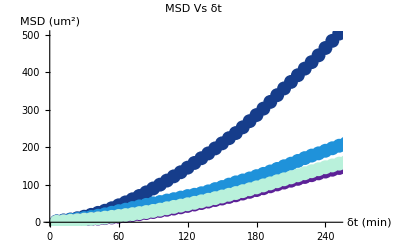

```mathematica
Show[ListPlot[Thread[{Range@Length@#*6,#*2*(0.633^2)}],PlotLabel->Style["MSD Vs δt",Bold,16],AxesLabel->{Style["δt (min)",{Bold,15}],Style["MSD (um^2)",{Bold,15}]},AxesStyle->Directive[Black, 14],PlotStyle->{RandomColor[],PointSize[0.025]},PlotRange->{{0,250},{0,500}}]&/@msds 
]
```

```mathematica
ListAnimate@MapThread[
HighlightImage[#1,{PointSize[0.005],Black,Point@{##2}},ImageSize->Medium]&,
{images[[58;;]],pos[[1]],pos[[2]],pos[[3]]}]
```

## pooled for two cases

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\trajectory in mosaic aggregates\\brachyury_trajectories.mx";
```

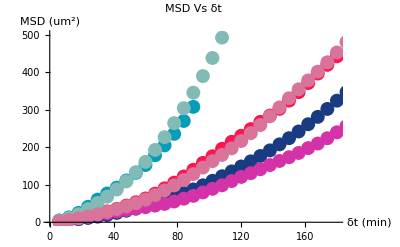

```mathematica
Show[ListPlot[Thread[{Range@Length@#*6,#*2*(0.633^2)}],PlotLabel->Style["MSD Vs δt",Bold,16],AxesLabel->{Style["δt (min)",{Bold,15}],Style["MSD (um^2)",{Bold,15}]},AxesStyle->Directive[Black, 14],PlotStyle->{RandomColor[],PointSize[0.025]},PlotRange->{{0,180},{0,500}}]&/@Drop[msds,-4] 
]
```

```mathematica
fit=SortBy[Cases[Thread[{Range@Length@#*6,#*2*(0.633^2)}]&/@Drop[msds,-4],{_?(#<180&),_},{2}],First];
sol=FindFit[MapAt[Log,fit,{All,2}],a x + b, {a,b},x]
```

{a→0.0233509,b→2.51965}

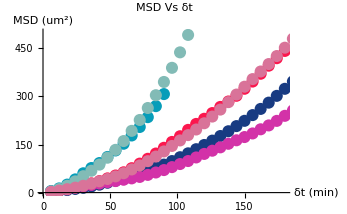
```mathematica
plt=-Graphics-;
```

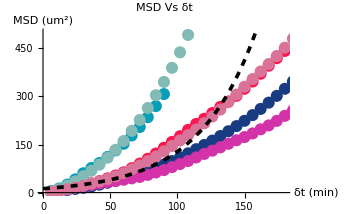

```mathematica
Show[plt,Plot[Evaluate[Exp[a x+b]/.sol],{x,0,180},PlotStyle->{Black,Thickness[0.0075],Dashed}]]
```